```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CloseKernels[];
LaunchKernels[18];
$KernelCount
```

18

# Produce data

```mathematica
sigma0=Import["../../sigma0.dat"];
sigma0p2=Import["../../sigma0p2.dat"];
mu=Table[i*5.,{i,1,80}];
mu2=Table[i,{i,290,310}];
T=Table[i,{i,1,300}];
pb1=Import["../../crossover.dat"];
pb2=Import["../../firstorder.dat"];
hin1=Import["h2/hdata1.dat"];
hin2=Import["h2/hdata2.dat"];
```

## quark mass depends on h

## equations

```mathematica
nff[mf2_,q_,T_,μ_]:=If[(√(q^2+mf2)-μ)/T>60.,0.,1/(Exp[(√(q^2+mf2)-μ)/T]+1)];
nfa[mf2_,q_,T_,μ_]:=If[(√(q^2+mf2)+μ)/T>60.,0.,1/(Exp[(√(q^2+mf2)+μ)/T]+1)];
nfd1xf[mf2_,q_,T_,μ_]:=(nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.))/T;
nfd2xf[mf2_,q_,T_,μ_]:=1/T^2 nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.)(2.*nff[mf2,q,T,μ]-1.);
nfd1xa[mf2_,q_,T_,μ_]:=(nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.))/T;
nfd2xa[mf2_,q_,T_,μ_]:=1/T^2 nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.)(2.*nfa[mf2,q,T,μ]-1.);
mf2[h_,ρ_]:=(h^2 ρ)/2;
dmf2d1rho[h_,ρ_]:=h^2/2;
dmf2d2rho[h_,ρ_]:=0;
Nf=2;
Nc=3;
V[ρ_,h_,T_,μ_,λ_,ν_,c_]:=1/(4 π^2)NIntegrate[4*Nc*Nf*q^4*2/3*1/(2 √(q^2+mf2[h,ρ]))(0-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]),{q,0,50.,100.,200.,500.,1000.,5000.}(*,AccuracyGoal->5,PrecisionGoal->5*),WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0,Method->{"GaussBerntsenEspelidRule","Points"->10}},MaxRecursion->10]+(λ/2 ρ^2+ν ρ)-c √(2ρ);
Vvacuum[ρ_,h_,M_]:=(Nc Nf)/1*mf2[h,ρ]^2/(8 π^2)(-Log[(√mf2[h,ρ])/M]);
Vd1rhovacuum[ρ_,h_,λ_,ν_,M_]:=-(Nc Nf dmf2d1rho[h,ρ] mf2[h,ρ])/(16 π^2)-(Nc Nf dmf2d1rho[h,ρ] Log[(√mf2[h,ρ])/M] mf2[h,ρ])/(4 π^2)+(λ ρ+ν);
Vd2rhovacuum[ρ_,h_,λ_,ν_,M_]:=-1/8 Nc Nf ((2 dmf2d1rho[h,ρ]^2)/π^2+((-dmf2d1rho[h,ρ]^2/(2 mf2[h,ρ]^2)+dmf2d2rho[h,ρ]/(2 mf2[h,ρ])) mf2[h,ρ]^2)/π^2+1/π^2 Log[(√mf2[h,ρ])/M] (2 dmf2d1rho[h,ρ]^2+2 dmf2d2rho[h,ρ] mf2[h,ρ]))+λ;
h=6.5;
λ300=75.8;
ν300=-482.^2;
c=1.7*10^-3*(10^3)^3;
M=300.;
F2[q_,ρ_,h_,T_,μ_]:=1/(4.*(q^2+mf2[h,ρ])^(3/2))(√(q^2+mf2[h,ρ])nfd1xa[mf2[h,ρ],q,T,μ]+√(q^2+mf2[h,ρ])nfd1xf[mf2[h,ρ],q,T,μ]+0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ])*q^3;
F3[q_,ρ_,h_,T_,μ_]:=q^5/(16.*(q^2+mf2[h,ρ])^(5/2))(-((q^2+mf2[h,ρ])(nfd2xf[mf2[h,ρ],q,T,μ]+nfd2xa[mf2[h,ρ],q,T,μ]))+3(√(q^2+mf2[h,ρ])*nfd1xf[mf2[h,ρ],q,T,μ]+√(q^2+mf2[h,ρ])*nfd1xa[mf2[h,ρ],q,T,μ]+0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]));
Zpsthr[ρ_,h_,T_,μ_]:=-2 h^2 Nc NIntegrate[1/(q 2 π^2)(-F2[q,ρ,h,T,μ]+2/3 F3[q,ρ,h,T,μ]),{q,0.,50.,100.,200.,500.,5000.}(*,{x,-1,1},{y,0,2π}*),
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->10];
Zpsvac[ρ_,h_,M_]:=-(Nc h^2)/(8 π^2)Log[(√mf2[h,ρ])/M];
Zps[ρ_,h_,T_,μ_,M_]:=Zpsthr[ρ,h,T,μ]+Zpsvac[ρ,h,M]+1.;
```

## h=6.5

```mathematica
Zdata=Table[ParallelTable[Zps[(sigma0[[j]][[i]])^2/2,hin1[[j]][[i]],N[i],mu[[j]],300.]//Quiet,{i,1,300}],{j,1,80}];
```

```mathematica
Zdatap2=Table[ParallelTable[Zps[(sigma0p2[[j]][[i]])^2/2,hin2[[j]][[i]],N[i],mu2[[j]],300.]//Quiet,{i,1,300}],{j,1,21}];
```

```mathematica
(*Export["./Zdata.dat",Zdata];
Export["./Zdatap2.dat",Zdatap2];*)
```

```mathematica
Zall=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,1,58}],1];
Zallp2=Flatten[Table[{x=mu2[[j]],y=T[[i]],Zdatap2[[j]][[i]]},{i,1,300},{j,1,21}],1];
Zallp3=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,62,80}],1];
```

```mathematica
phaseplot=Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["M=300 MeV with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->Pink,PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Red,PointSize[Medium]}(*,PlotLegends->{"CEP"}*)]],ImageResolution->300]
```

-Graphics-

```mathematica
phaseplot=
Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},ColorFunction->(Blend[{Blue,White,Red},Rescale[#,{-2,2}]]&),ColorFunctionScaling->False,FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["Z_π^⊥(p=0;T=0,μ=0)=1 with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->{Black,Opacity[0.1]},PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Black,PointSize[Medium]}]],ImageResolution->300]
```

-Graphics-

```mathematica
(*Export["phaseQCDinput.pdf",phaseplot];*)
```

## h=7.5

```mathematica
Zdata=Table[ParallelTable[Zps[(sigma0[[j]][[i]])^2/2,hin1[[j]][[i]]-6.5+7.5,N[i],mu[[j]],300.]//Quiet,{i,1,300}],{j,1,80}];
```

```mathematica
Zdatap2=Table[ParallelTable[Zps[(sigma0p2[[j]][[i]])^2/2,hin2[[j]][[i]]-6.5+7.5,N[i],mu2[[j]],300.]//Quiet,{i,1,300}],{j,1,21}];
```

```mathematica
(*Export["./Zdata.dat",Zdata];
Export["./Zdatap2.dat",Zdatap2];*)
```

```mathematica
Zall=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,1,58}],1];
Zallp2=Flatten[Table[{x=mu2[[j]],y=T[[i]],Zdatap2[[j]][[i]]},{i,1,300},{j,1,21}],1];
Zallp3=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,62,80}],1];
```

```mathematica
phaseplot=Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["M=300 MeV with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->Pink,PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Red,PointSize[Medium]}(*,PlotLegends->{"CEP"}*)]],ImageResolution->300]
```

-Graphics-

```mathematica
phaseplot=
Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},ColorFunction->(Blend[{Blue,White,Red},Rescale[#,{-2,2}]]&),ColorFunctionScaling->False,FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["Z_π^⊥(p=0;T=0,μ=0)=1 with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->{Black,Opacity[0.1]},PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Black,PointSize[Medium]}]],ImageResolution->300]
```

-Graphics-

```mathematica
(*Export["phaseQCDinput.pdf",phaseplot];*)
```

## h=8.5

```mathematica
Zdata=Table[ParallelTable[Zps[(sigma0[[j]][[i]])^2/2,hin1[[j]][[i]]-6.5+8.5,N[i],mu[[j]],300.]//Quiet,{i,1,300}],{j,1,80}];
```

```mathematica
Zdatap2=Table[ParallelTable[Zps[(sigma0p2[[j]][[i]])^2/2,hin2[[j]][[i]]-6.5+8.5,N[i],mu2[[j]],300.]//Quiet,{i,1,300}],{j,1,21}];
```

```mathematica
Zall=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,1,58}],1];
Zallp2=Flatten[Table[{x=mu2[[j]],y=T[[i]],Zdatap2[[j]][[i]]},{i,1,300},{j,1,21}],1];
Zallp3=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,62,80}],1];
```

```mathematica
phaseplot=Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["M=300 MeV with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->Pink,PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Red,PointSize[Medium]}(*,PlotLegends->{"CEP"}*)]],ImageResolution->300]
```

-Graphics-

```mathematica
phaseplot=
Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},ColorFunction->(Blend[{Blue,White,Red},Rescale[#,{-2,2}]]&),ColorFunctionScaling->False,FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["Z_π^⊥(p=0;T=0,μ=0)=1 with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->{Black,Opacity[0.1]},PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Black,PointSize[Medium]}]],ImageResolution->300]
```

-Graphics-

```mathematica
(*Export["phaseQCDinput.pdf",phaseplot];*)
```

## h=9.5

```mathematica
Zdata=Table[ParallelTable[Zps[(sigma0[[j]][[i]])^2/2,hin1[[j]][[i]]-6.5+9.5,N[i],mu[[j]],300.]//Quiet,{i,1,300}],{j,1,80}];
```

```mathematica
Zdatap2=Table[ParallelTable[Zps[(sigma0p2[[j]][[i]])^2/2,hin2[[j]][[i]]-6.5+9.5,N[i],mu2[[j]],300.]//Quiet,{i,1,300}],{j,1,21}];
```

```mathematica
Zall=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,1,58}],1];
Zallp2=Flatten[Table[{x=mu2[[j]],y=T[[i]],Zdatap2[[j]][[i]]},{i,1,300},{j,1,21}],1];
Zallp3=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,62,80}],1];
```

```mathematica
phaseplot=Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["M=300 MeV with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->Pink,PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Red,PointSize[Medium]}(*,PlotLegends->{"CEP"}*)]],ImageResolution->300]
```

-Graphics-

```mathematica
phaseplot=
Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},ColorFunction->(Blend[{Blue,White,Red},Rescale[#,{-2,2}]]&),ColorFunctionScaling->False,FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["Z_π^⊥(p=0;T=0,μ=0)=1 with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->{Black,Opacity[0.1]},PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Black,PointSize[Medium]}]],ImageResolution->300]
```

-Graphics-

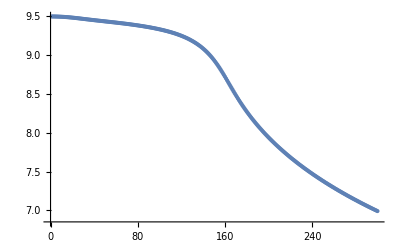

```mathematica
ListPlot[hin1[[1]]-6.5+9.5]
```

```mathematica
(*Export["phaseQCDinput.pdf",phaseplot];*)
```

## h=9.5 constant

```mathematica
Zdata=Table[ParallelTable[Zps[(sigma0[[j]][[i]])^2/2,9.5,N[i],mu[[j]],300.]//Quiet,{i,1,300}],{j,1,80}];
```

```mathematica
Zdatap2=Table[ParallelTable[Zps[(sigma0p2[[j]][[i]])^2/2,9.5,N[i],mu2[[j]],300.]//Quiet,{i,1,300}],{j,1,21}];
```

```mathematica
Zall=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,1,58}],1];
Zallp2=Flatten[Table[{x=mu2[[j]],y=T[[i]],Zdatap2[[j]][[i]]},{i,1,300},{j,1,21}],1];
Zallp3=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,62,80}],1];
```

```mathematica
phaseplot=Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["M=300 MeV with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->Pink,PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Red,PointSize[Medium]}(*,PlotLegends->{"CEP"}*)]],ImageResolution->300]
```

-Graphics-

```mathematica
phaseplot=
Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},ColorFunction->(Blend[{Blue,White,Red},Rescale[#,{-2,2}]]&),ColorFunctionScaling->False,FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["Z_π^⊥(p=0;T=0,μ=0)=1 with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->{Black,Opacity[0.1]},PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Black,PointSize[Medium]}]],ImageResolution->300]
```

-Graphics-

```mathematica
ListPlot[hin1[[1]]-6.5+9.5]
```

-Graphics-

```mathematica
(*Export["phaseQCDinput.pdf",phaseplot];*)
```

## quark mass h=6.5

## equations

```mathematica
nff[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)-μ)/T]+1);
nfa[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)+μ)/T]+1);
nfd1xf[mf2_,q_,T_,μ_]:=(nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.))/T;
nfd2xf[mf2_,q_,T_,μ_]:=1/T^2 nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.)(2.*nff[mf2,q,T,μ]-1.);
nfd1xa[mf2_,q_,T_,μ_]:=(nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.))/T;
nfd2xa[mf2_,q_,T_,μ_]:=1/T^2 nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.)(2.*nfa[mf2,q,T,μ]-1.);
mf2[h_,ρ_]:=(h^2 ρ)/2;
dmf2d1rho[h_,ρ_]:=h^2/2;
dmf2d2rho[h_,ρ_]:=0;
Nf=2;
Nc=3;
V[ρ_,h_,T_,μ_,λ_,ν_,c_]:=1/(4 π^2)NIntegrate[4*Nc*Nf*q^4*2/3*1/(2 √(q^2+mf2[h,ρ]))(0-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]),{q,0,50.,100.,200.,500.,1000.,5000.}(*,AccuracyGoal->5,PrecisionGoal->5*),WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0,Method->{"GaussBerntsenEspelidRule","Points"->10}},MaxRecursion->10]+(λ/2 ρ^2+ν ρ)-c √(2ρ);
Vvacuum[ρ_,h_,M_]:=(Nc Nf)/1*mf2[h,ρ]^2/(8 π^2)(-Log[(√mf2[h,ρ])/M]);
Vd1rhovacuum[ρ_,h_,λ_,ν_,M_]:=-(Nc Nf dmf2d1rho[h,ρ] mf2[h,ρ])/(16 π^2)-(Nc Nf dmf2d1rho[h,ρ] Log[(√mf2[h,ρ])/M] mf2[h,ρ])/(4 π^2)+(λ ρ+ν);
Vd2rhovacuum[ρ_,h_,λ_,ν_,M_]:=-1/8 Nc Nf ((2 dmf2d1rho[h,ρ]^2)/π^2+((-dmf2d1rho[h,ρ]^2/(2 mf2[h,ρ]^2)+dmf2d2rho[h,ρ]/(2 mf2[h,ρ])) mf2[h,ρ]^2)/π^2+1/π^2 Log[(√mf2[h,ρ])/M] (2 dmf2d1rho[h,ρ]^2+2 dmf2d2rho[h,ρ] mf2[h,ρ]))+λ;
h=6.5;
λ300=75.8;
ν300=-482.^2;
c=1.7*10^-3*(10^3)^3;
M=300.;
F2[q_,ρ_,h_,T_,μ_]:=1/(4.*(q^2+mf2[h,ρ])^(3/2))(√(q^2+mf2[h,ρ])nfd1xa[mf2[h,ρ],q,T,μ]+√(q^2+mf2[h,ρ])nfd1xf[mf2[h,ρ],q,T,μ]+0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ])*q^3;
F3[q_,ρ_,h_,T_,μ_]:=q^5/(16.*(q^2+mf2[h,ρ])^(5/2))(-((q^2+mf2[h,ρ])(nfd2xf[mf2[h,ρ],q,T,μ]+nfd2xa[mf2[h,ρ],q,T,μ]))+3(√(q^2+mf2[h,ρ])*nfd1xf[mf2[h,ρ],q,T,μ]+√(q^2+mf2[h,ρ])*nfd1xa[mf2[h,ρ],q,T,μ]+0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]));
Zpsthr[ρ_,h_,T_,μ_]:=-2 h^2 Nc NIntegrate[1/(q 2 π^2)(-F2[q,ρ,6.5,T,μ]+2/3 F3[q,ρ,6.5,T,μ]),{q,0.,50.,100.,200.,500.,5000.}(*,{x,-1,1},{y,0,2π}*),
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->10];
Zpsvac[ρ_,h_,M_]:=-(Nc h^2)/(8 π^2)Log[(√mf2[6.5,ρ])/M];
Zps[ρ_,h_,T_,μ_,M_]:=Zpsthr[ρ,h,T,μ]+Zpsvac[ρ,h,M]+1.;
```

## h=6.5

```mathematica
Zdata=Table[ParallelTable[Zps[(sigma0[[j]][[i]])^2/2,hin1[[j]][[i]],N[i],mu[[j]],300.]//Quiet,{i,1,300}],{j,1,80}];
Zdatap2=Table[ParallelTable[Zps[(sigma0p2[[j]][[i]])^2/2,hin2[[j]][[i]],N[i],mu2[[j]],300.]//Quiet,{i,1,300}],{j,1,21}];
```

```mathematica
Zall=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,1,58}],1];
Zallp2=Flatten[Table[{x=mu2[[j]],y=T[[i]],Zdatap2[[j]][[i]]},{i,1,300},{j,1,21}],1];
Zallp3=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,62,80}],1];
```

```mathematica
phaseplot=Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["M=300 MeV with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->Pink,PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Red,PointSize[Medium]}(*,PlotLegends->{"CEP"}*)]],ImageResolution->300]
```

-Graphics-

```mathematica
phaseplot=
Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},ColorFunction->(Blend[{Blue,White,Red},Rescale[#,{-2,2}]]&),ColorFunctionScaling->False,FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["Z_π^⊥(p=0;T=0,μ=0)=1 with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->{Black,Opacity[0.1]},PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Black,PointSize[Medium]}]],ImageResolution->300]
```

-Graphics-

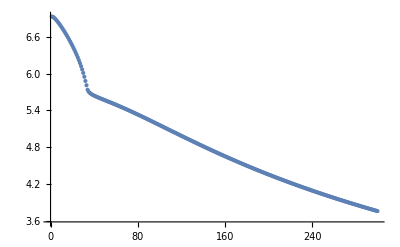

```mathematica
ListPlot[hin1[[59]]]
```

```mathematica
(*Export["phaseQCDinput.pdf",phaseplot];*)
```

## h=7.0

```mathematica
Zdata=Table[ParallelTable[Zps[(sigma0[[j]][[i]])^2/2,hin1[[j]][[i]]-6.5+7.0,N[i],mu[[j]],300.]//Quiet,{i,1,300}],{j,1,80}];
Zdatap2=Table[ParallelTable[Zps[(sigma0p2[[j]][[i]])^2/2,hin2[[j]][[i]]-6.5+7.0,N[i],mu2[[j]],300.]//Quiet,{i,1,300}],{j,1,21}];
```

```mathematica
Zall=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,1,58}],1];
Zallp2=Flatten[Table[{x=mu2[[j]],y=T[[i]],Zdatap2[[j]][[i]]},{i,1,300},{j,1,21}],1];
Zallp3=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,62,80}],1];
```

```mathematica
phaseplot=
Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},ColorFunction->(Blend[{Blue,White,Red},Rescale[#,{-2,2}]]&),ColorFunctionScaling->False,FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["Z_π^⊥(p=0;T=0,μ=0)=1 with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->{Black,Opacity[0.1]},PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Black,PointSize[Medium]}]],ImageResolution->300]
```

-Graphics-

## h=7.5

```mathematica
Zdata=Table[ParallelTable[Zps[(sigma0[[j]][[i]])^2/2,hin1[[j]][[i]]-6.5+7.5,N[i],mu[[j]],300.]//Quiet,{i,1,300}],{j,1,80}];
Zdatap2=Table[ParallelTable[Zps[(sigma0p2[[j]][[i]])^2/2,hin2[[j]][[i]]-6.5+7.5,N[i],mu2[[j]],300.]//Quiet,{i,1,300}],{j,1,21}];
```

```mathematica
Zall=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,1,58}],1];
Zallp2=Flatten[Table[{x=mu2[[j]],y=T[[i]],Zdatap2[[j]][[i]]},{i,1,300},{j,1,21}],1];
Zallp3=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,62,80}],1];
```

```mathematica
phaseplot=
Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},ColorFunction->(Blend[{Blue,White,Red},Rescale[#,{-2,2}]]&),ColorFunctionScaling->False,FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["Z_π^⊥(p=0;T=0,μ=0)=1 with Yukawa coupling",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{(*-0.185,*)0.(*,0.32,0.415,0.48*)}},MeshStyle->{Black,Opacity[0.3]},PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,Epilog->{Text[Style["h=7.0",Black,14],{370,20}],Text[Style["h=7.5",Black,14],{360,100}],Text[Style["h=8.5",Black,14],{375,250}],Text[Style["h=9.0",Black,14],{295,250}],Text[Style["h=9.5",Black,14],{130,250}]},FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Black,PointSize[Medium]}],ListLinePlot[pb1,PlotStyle->{Black,Dashed,Opacity[0.2]}],ListLinePlot[pb2,PlotStyle->{Black,Opacity[0.1]}]],ImageResolution->300]
```

-Graphics-

```mathematica
Export["phaseyukawainput.pdf",phaseplot];
```

## h=8.5

```mathematica
Zdata=Table[ParallelTable[Zps[(sigma0[[j]][[i]])^2/2,hin1[[j]][[i]]-6.5+8.5,N[i],mu[[j]],300.]//Quiet,{i,1,300}],{j,1,80}];
Zdatap2=Table[ParallelTable[Zps[(sigma0p2[[j]][[i]])^2/2,hin2[[j]][[i]]-6.5+8.5,N[i],mu2[[j]],300.]//Quiet,{i,1,300}],{j,1,21}];
```

```mathematica
Zall=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,1,58}],1];
Zallp2=Flatten[Table[{x=mu2[[j]],y=T[[i]],Zdatap2[[j]][[i]]},{i,1,300},{j,1,21}],1];
Zallp3=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,62,80}],1];
```

```mathematica
phaseplot=Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["M=300 MeV with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->Pink,PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Red,PointSize[Medium]}(*,PlotLegends->{"CEP"}*)]],ImageResolution->300]
```

-Graphics-

```mathematica
phaseplot=
Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},ColorFunction->(Blend[{Blue,White,Red},Rescale[#,{-2,2}]]&),ColorFunctionScaling->False,FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["Z_π^⊥(p=0;T=0,μ=0)=1 with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->{Black,Opacity[0.1]},PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Black,PointSize[Medium]}]],ImageResolution->300]
```

-Graphics-

```mathematica
(*Export["phaseQCDinput.pdf",phaseplot];*)
```

## h=9.0

```mathematica
Zdata=Table[ParallelTable[Zps[(sigma0[[j]][[i]])^2/2,hin1[[j]][[i]]-6.5+9.0,N[i],mu[[j]],300.]//Quiet,{i,1,300}],{j,1,80}];
Zdatap2=Table[ParallelTable[Zps[(sigma0p2[[j]][[i]])^2/2,hin2[[j]][[i]]-6.5+9.0,N[i],mu2[[j]],300.]//Quiet,{i,1,300}],{j,1,21}];
```

```mathematica
Zall=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,1,58}],1];
Zallp2=Flatten[Table[{x=mu2[[j]],y=T[[i]],Zdatap2[[j]][[i]]},{i,1,300},{j,1,21}],1];
Zallp3=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,62,80}],1];
```

```mathematica
phaseplot=Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["M=300 MeV with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->Pink,PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Red,PointSize[Medium]}(*,PlotLegends->{"CEP"}*)]],ImageResolution->300]
```

-Graphics-

```mathematica
phaseplot=
Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},ColorFunction->(Blend[{Blue,White,Red},Rescale[#,{-2,2}]]&),ColorFunctionScaling->False,FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["Z_π^⊥(p=0;T=0,μ=0)=1 with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->{Black,Opacity[0.1]},PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Black,PointSize[Medium]}]],ImageResolution->300]
```

-Graphics-

```mathematica
(*Export["phaseQCDinput.pdf",phaseplot];*)
```

## h=9.5

```mathematica
Zdata=Table[ParallelTable[Zps[(sigma0[[j]][[i]])^2/2,hin1[[j]][[i]]-6.5+9.5,N[i],mu[[j]],300.]//Quiet,{i,1,300}],{j,1,80}];
Zdatap2=Table[ParallelTable[Zps[(sigma0p2[[j]][[i]])^2/2,hin2[[j]][[i]]-6.5+9.5,N[i],mu2[[j]],300.]//Quiet,{i,1,300}],{j,1,21}];
```

```mathematica
Zall=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,1,58}],1];
Zallp2=Flatten[Table[{x=mu2[[j]],y=T[[i]],Zdatap2[[j]][[i]]},{i,1,300},{j,1,21}],1];
Zallp3=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,62,80}],1];
```

```mathematica
phaseplot=Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["M=300 MeV with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->Pink,PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Red,PointSize[Medium]}(*,PlotLegends->{"CEP"}*)]],ImageResolution->300]
```

-Graphics-

```mathematica
phaseplot=
Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},ColorFunction->(Blend[{Blue,White,Red},Rescale[#,{-2,2}]]&),ColorFunctionScaling->False,FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["Z_π^⊥(p=0;T=0,μ=0)=1 with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->{Black,Opacity[0.1]},PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Black,PointSize[Medium]}]],ImageResolution->300]
```

-Graphics-

```mathematica
(*Export["phaseQCDinput.pdf",phaseplot];*)
```

## h=9.5 constant

```mathematica
Zdata=Table[ParallelTable[Zps[(sigma0[[j]][[i]])^2/2,9.5,N[i],mu[[j]],300.]//Quiet,{i,1,300}],{j,1,80}];
Zdatap2=Table[ParallelTable[Zps[(sigma0p2[[j]][[i]])^2/2,9.5,N[i],mu2[[j]],300.]//Quiet,{i,1,300}],{j,1,21}];
```

```mathematica
Zall=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,1,58}],1];
Zallp2=Flatten[Table[{x=mu2[[j]],y=T[[i]],Zdatap2[[j]][[i]]},{i,1,300},{j,1,21}],1];
Zallp3=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,62,80}],1];
```

```mathematica
phaseplot=Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["M=300 MeV with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->Pink,PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Red,PointSize[Medium]}(*,PlotLegends->{"CEP"}*)]],ImageResolution->300]
```

-Graphics-

```mathematica
phaseplot=
Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},ColorFunction->(Blend[{Blue,White,Red},Rescale[#,{-2,2}]]&),ColorFunctionScaling->False,FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["Z_π^⊥(p=0;T=0,μ=0)=1 with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->{Black,Opacity[0.1]},PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Black,PointSize[Medium]}]],ImageResolution->300]
```

-Graphics-

```mathematica
(*Export["phaseQCDinput.pdf",phaseplot];*)
```

## quark mass h=6.5 and h(T,μ=0)

## equations

```mathematica
nff[mf2_,q_,T_,μ_]:=If[(√(q^2+mf2)-μ)/T>60.,0.,1/(Exp[(√(q^2+mf2)-μ)/T]+1)];
nfa[mf2_,q_,T_,μ_]:=If[(√(q^2+mf2)+μ)/T>60.,0.,1/(Exp[(√(q^2+mf2)+μ)/T]+1)];
nfd1xf[mf2_,q_,T_,μ_]:=(nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.))/T;
nfd2xf[mf2_,q_,T_,μ_]:=1/T^2 nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.)(2.*nff[mf2,q,T,μ]-1.);
nfd1xa[mf2_,q_,T_,μ_]:=(nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.))/T;
nfd2xa[mf2_,q_,T_,μ_]:=1/T^2 nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.)(2.*nfa[mf2,q,T,μ]-1.);
mf2[h_,ρ_]:=(h^2 ρ)/2;
dmf2d1rho[h_,ρ_]:=h^2/2;
dmf2d2rho[h_,ρ_]:=0;
Nf=2;
Nc=3;
V[ρ_,h_,T_,μ_,λ_,ν_,c_]:=1/(4 π^2)NIntegrate[4*Nc*Nf*q^4*2/3*1/(2 √(q^2+mf2[h,ρ]))(0-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]),{q,0,50.,100.,200.,500.,1000.,5000.}(*,AccuracyGoal->5,PrecisionGoal->5*),WorkingPrecision->10,Method->{"GlobalAdaptive","SymbolicProcessing"->0,Method->{"GaussBerntsenEspelidRule","Points"->10}},MaxRecursion->10]+(λ/2 ρ^2+ν ρ)-c √(2ρ);
Vvacuum[ρ_,h_,M_]:=(Nc Nf)/1*mf2[h,ρ]^2/(8 π^2)(-Log[(√mf2[h,ρ])/M]);
Vd1rhovacuum[ρ_,h_,λ_,ν_,M_]:=-(Nc Nf dmf2d1rho[h,ρ] mf2[h,ρ])/(16 π^2)-(Nc Nf dmf2d1rho[h,ρ] Log[(√mf2[h,ρ])/M] mf2[h,ρ])/(4 π^2)+(λ ρ+ν);
Vd2rhovacuum[ρ_,h_,λ_,ν_,M_]:=-1/8 Nc Nf ((2 dmf2d1rho[h,ρ]^2)/π^2+((-dmf2d1rho[h,ρ]^2/(2 mf2[h,ρ]^2)+dmf2d2rho[h,ρ]/(2 mf2[h,ρ])) mf2[h,ρ]^2)/π^2+1/π^2 Log[(√mf2[h,ρ])/M] (2 dmf2d1rho[h,ρ]^2+2 dmf2d2rho[h,ρ] mf2[h,ρ]))+λ;
h=6.5;
λ300=75.8;
ν300=-482.^2;
c=1.7*10^-3*(10^3)^3;
M=300.;
F2[q_,ρ_,h_,T_,μ_]:=1/(4.*(q^2+mf2[h,ρ])^(3/2))(√(q^2+mf2[h,ρ])nfd1xa[mf2[h,ρ],q,T,μ]+√(q^2+mf2[h,ρ])nfd1xf[mf2[h,ρ],q,T,μ]+0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ])*q^3;
F3[q_,ρ_,h_,T_,μ_]:=q^5/(16.*(q^2+mf2[h,ρ])^(5/2))(-((q^2+mf2[h,ρ])(nfd2xf[mf2[h,ρ],q,T,μ]+nfd2xa[mf2[h,ρ],q,T,μ]))+3(√(q^2+mf2[h,ρ])*nfd1xf[mf2[h,ρ],q,T,μ]+√(q^2+mf2[h,ρ])*nfd1xa[mf2[h,ρ],q,T,μ]+0.-nff[mf2[h,ρ],q,T,μ]-nfa[mf2[h,ρ],q,T,μ]));
Zpsthr[ρ_,h_,T_,μ_]:=-2 h^2 Nc NIntegrate[1/(q 2 π^2)(-F2[q,ρ,6.5,T,μ]+2/3 F3[q,ρ,6.5,T,μ]),{q,0.,50.,100.,200.,500.,5000.}(*,{x,-1,1},{y,0,2π}*),
Method->{"GlobalAdaptive","SymbolicProcessing"->0(*,Method->{"GaussBerntsenEspelidRule","Points"->10}*)},MaxRecursion->10];
Zpsvac[ρ_,h_,M_]:=-(Nc h^2)/(8 π^2)Log[(√mf2[6.5,ρ])/M];
Zps[ρ_,h_,T_,μ_,M_]:=Zpsthr[ρ,h,T,μ]+Zpsvac[ρ,h,M]+1.;
```

## h=6.5

```mathematica
Zdata=Table[ParallelTable[Zps[(sigma0[[j]][[i]])^2/2,hin1[[1]][[i]],N[i],mu[[j]],300.]//Quiet,{i,1,300}],{j,1,80}];
Zdatap2=Table[ParallelTable[Zps[(sigma0p2[[j]][[i]])^2/2,hin1[[1]][[i]],N[i],mu2[[j]],300.]//Quiet,{i,1,300}],{j,1,21}];
```

```mathematica
Zall=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,1,58}],1];
Zallp2=Flatten[Table[{x=mu2[[j]],y=T[[i]],Zdatap2[[j]][[i]]},{i,1,300},{j,1,21}],1];
Zallp3=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,62,80}],1];
```

```mathematica
phaseplot=Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["M=300 MeV with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->Pink,PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Red,PointSize[Medium]}(*,PlotLegends->{"CEP"}*)]],ImageResolution->300]
```

-Graphics-

```mathematica
phaseplot=
Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},ColorFunction->(Blend[{Blue,White,Red},Rescale[#,{-2,2}]]&),ColorFunctionScaling->False,FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["Z_π^⊥(p=0;T=0,μ=0)=1 with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->{Black,Opacity[0.1]},PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Black,PointSize[Medium]}]],ImageResolution->300]
```

-Graphics-

```mathematica
(*Export["phaseQCDinput.pdf",phaseplot];*)
```

## h=7.5

```mathematica
Zdata=Table[ParallelTable[Zps[(sigma0[[j]][[i]])^2/2,hin1[[1]][[i]]-6.5+7.5,N[i],mu[[j]],300.]//Quiet,{i,1,300}],{j,1,80}];
Zdatap2=Table[ParallelTable[Zps[(sigma0p2[[j]][[i]])^2/2,hin1[[1]][[i]]-6.5+7.5,N[i],mu2[[j]],300.]//Quiet,{i,1,300}],{j,1,21}];
```

```mathematica
Zall=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,1,58}],1];
Zallp2=Flatten[Table[{x=mu2[[j]],y=T[[i]],Zdatap2[[j]][[i]]},{i,1,300},{j,1,21}],1];
Zallp3=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,62,80}],1];
```

```mathematica
phaseplot=Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["M=300 MeV with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->Pink,PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Red,PointSize[Medium]}(*,PlotLegends->{"CEP"}*)]],ImageResolution->300]
```

-Graphics-

```mathematica
phaseplot=
Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},ColorFunction->(Blend[{Blue,White,Red},Rescale[#,{-2,2}]]&),ColorFunctionScaling->False,FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["Z_π^⊥(p=0;T=0,μ=0)=1 with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->{Black,Opacity[0.1]},PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Black,PointSize[Medium]}]],ImageResolution->300]
```

-Graphics-

```mathematica
(*Export["phaseQCDinput.pdf",phaseplot];*)
```

## h=8.5

```mathematica
Zdata=Table[ParallelTable[Zps[(sigma0[[j]][[i]])^2/2,hin1[[1]][[i]]-6.5+8.5,N[i],mu[[j]],300.]//Quiet,{i,1,300}],{j,1,80}];
Zdatap2=Table[ParallelTable[Zps[(sigma0p2[[j]][[i]])^2/2,hin1[[1]][[i]]-6.5+8.5,N[i],mu2[[j]],300.]//Quiet,{i,1,300}],{j,1,21}];
```

```mathematica
Zall=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,1,58}],1];
Zallp2=Flatten[Table[{x=mu2[[j]],y=T[[i]],Zdatap2[[j]][[i]]},{i,1,300},{j,1,21}],1];
Zallp3=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,62,80}],1];
```

```mathematica
phaseplot=Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["M=300 MeV with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->Pink,PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Red,PointSize[Medium]}(*,PlotLegends->{"CEP"}*)]],ImageResolution->300]
```

-Graphics-

```mathematica
phaseplot=
Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},ColorFunction->(Blend[{Blue,White,Red},Rescale[#,{-2,2}]]&),ColorFunctionScaling->False,FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["Z_π^⊥(p=0;T=0,μ=0)=1 with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->{Black,Opacity[0.1]},PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Black,PointSize[Medium]}]],ImageResolution->300]
```

-Graphics-

```mathematica
(*Export["phaseQCDinput.pdf",phaseplot];*)
```

## h=9.5

```mathematica
Zdata=Table[ParallelTable[Zps[(sigma0[[j]][[i]])^2/2,hin1[[1]][[i]]-6.5+9.5,N[i],mu[[j]],300.]//Quiet,{i,1,300}],{j,1,80}];
Zdatap2=Table[ParallelTable[Zps[(sigma0p2[[j]][[i]])^2/2,hin1[[1]][[i]]-6.5+9.5,N[i],mu2[[j]],300.]//Quiet,{i,1,300}],{j,1,21}];
```

```mathematica
Zall=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,1,58}],1];
Zallp2=Flatten[Table[{x=mu2[[j]],y=T[[i]],Zdatap2[[j]][[i]]},{i,1,300},{j,1,21}],1];
Zallp3=Flatten[Table[{x=mu[[j]],y=T[[i]],Zdata[[j]][[i]]},{i,1,300},{j,62,80}],1];
```

```mathematica
phaseplot=Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["M=300 MeV with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->Pink,PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Red,PointSize[Medium]}(*,PlotLegends->{"CEP"}*)]],ImageResolution->300]
```

-Graphics-

```mathematica
phaseplot=
Rasterize[Show[ListDensityPlot[{Zall,Zallp2,Zallp3},ColorFunction->(Blend[{Blue,White,Red},Rescale[#,{-2,2}]]&),ColorFunctionScaling->False,FrameLabel->{Style["μ [MeV]",Black,15,FontFamily->"Times New Roman"],Style["T [MeV]",Black,15,FontFamily->"Times New Roman"],Style["Z_π^⊥(p=0;T=0,μ=0)=1 with QCD input",Black,15,FontFamily->"Times New Roman"]},PlotLegends->Automatic,LabelStyle->{Black,12},MeshFunctions->{#3&},Mesh->{{0.}},MeshStyle->{Black,Opacity[0.1]},PlotRange->All,InterpolationOrder->1,AspectRatio->3/4,FrameStyle->Directive[Black,Thickness[0.003]]],ListPlot[{{296,31}},PlotStyle->{Black,PointSize[Medium]}]],ImageResolution->300]
```

-Graphics-

```mathematica
(*Export["phaseQCDinput.pdf",phaseplot];*)
```